Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

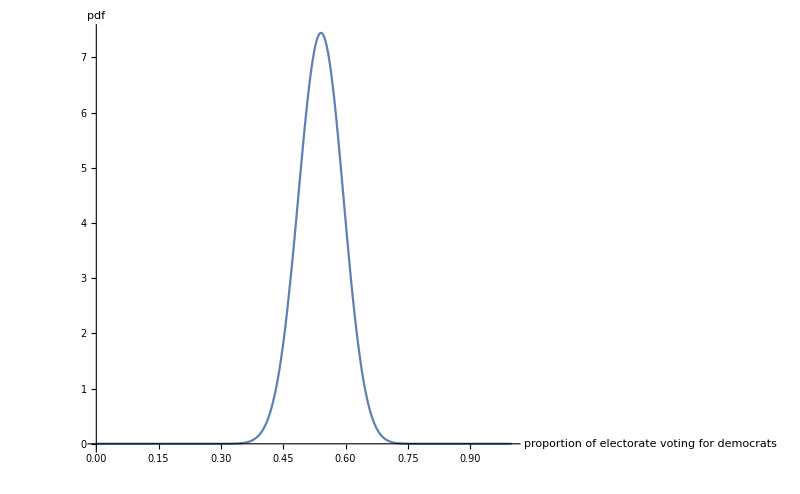

```mathematica
μ = 0.54;
σ = 0.2;
β1 = 40;
Clear[α,β]
α=(α/.Solve[α/(α+β)==μ,α]/.{β->β1})[[1]];
Show[Plot[PDF[BetaDistribution[α,β1],x],{x,0,1},PlotRange->Full,AxesLabel->{"proportion of electorate voting for democrats ","pdf "},BaseStyle->{FontSize->16}],ImageSize->800]
```

```mathematica
β=β1;
Sqrt[Variance[BetaDistribution[α,β1]]]
```

0.0531425

```mathematica
StandardDeviation[BetaDistribution[α,β1]]
```

0.0531425